```mathematica
ImagePartition[GeoGraphics[Here, GeoRange->Quantity[0.5,"Miles"]], 150]//Grid
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
GeoEntities[GeoDisk[Entity["City",{"NewYork","NewYork","UnitedStates"}],Quantity[2,"Kilometers"]],"Building"]
```

{770 Eastern Parkway,Church of Our Lady of Victory,Church of Saint Francis of Assisi and Saint Blaise,St. Blaise's Church}

```mathematica
analyzeCityTiles[cityEntity_,tileSize_,entityType_]:=Module[{center,region,bounds,latRange,lonRange,latStep,lonStep,latitudes,longitudes,tileBoxes,tileFeatures},(*Get the city's geographic center*)center=EntityValue[cityEntity,"Position"];
(*Define analysis region around center (1 km radius)*)region=GeoDisk[center,Quantity[1,"Kilometers"]];
bounds=GeoBounds[region];
(*Approximate tile step sizes in degrees*)latStep=QuantityMagnitude@GeoDistance[GeoPosition[{bounds[[1,1]],bounds[[1,2]]}],GeoPosition[{bounds[[1,1]]+0.005,bounds[[1,2]]}]];
lonStep=QuantityMagnitude@GeoDistance[GeoPosition[{bounds[[1,1]],bounds[[1,2]]}],GeoPosition[{bounds[[1,1]],bounds[[1,2]]+0.005}]];
(*Create latitude and longitude grid*)latitudes=Range[bounds[[1,1]],bounds[[2,1]],tileSize/111320.];(*1 deg≈111.32 km*)longitudes=Range[bounds[[1,2]],bounds[[2,2]],tileSize/111320.];
(*Build tiles centered at lat/lon grid points*)tileBoxes=Flatten[Table[GeoBoundingBox[GeoPosition[{lat,lon}],Quantity[tileSize/2,"Meters"]],{lat,latitudes},{lon,longitudes}],1];
(*Count and extract entities in each tile*)tileFeatures=Table[With[{entities=Quiet@GeoEntities[tileBoxes[[i]],entityType]},<|"TileIndex"->i,"BoundingBox"->tileBoxes[[i]],"EntityCount"->Length[entities],"EntityPositions"->Quiet@EntityValue[entities,"Position"]|>],{i,Length[tileBoxes]}];
Dataset[tileFeatures]]

boston=Entity["City",{"Boston","Massachusetts","UnitedStates"}];
analyzeCityTiles[boston,500,"Building"]
```

```mathematica
cityEntity = Entity["City",{"Boston","Massachusetts","UnitedStates"}]; (*Boston*) 
tileSize = 500;
entityType = "Building";
center=EntityValue[cityEntity,"Position"];
region=GeoDisk[center,Quantity[1,"Kilometers"]];
bounds=GeoBounds[region];
```

500

Building

```mathematica
osm=OSMImport[GeoBoundsRegion[{{40.0923,40.0991},{-48.2586,-48.2479}}]];
```

```mathematica
(*Step 1:Load the region*)openStreetMapRegion=ResourceFunction["OSMImport"][GeoBoundsRegion[{{40.755905,40.769988},{-73.994486,-73.968818}}]];



(*(*Step 2:Filter for roads only*)
roadWays=Select[openStreetMapRegion["Ways"],MatchQ[#[["Tags","highway"]],"residential"|"primary"|"secondary"|"tertiary"|"motorway"|"trunk"]&];

(*Step 3:Build Line graphics primitives from node coordinates*)
roadLines=Line[openStreetMapRegion[["Nodes",#Nodes,"Position"]]]&/@roadWays;*)
```

```mathematica
Line[Values[openStreetMapRegion[["Nodes",#Nodes,"Position"]]]]&/@Select[openStreetMapRegion["Ways"],MatchQ[#[["Tags","highway"]],"residential"]&]
```

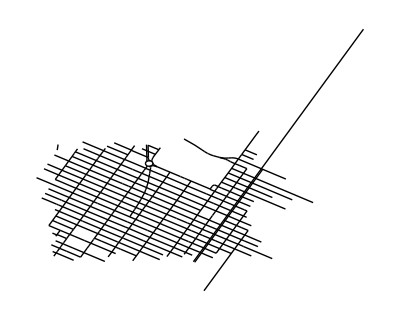

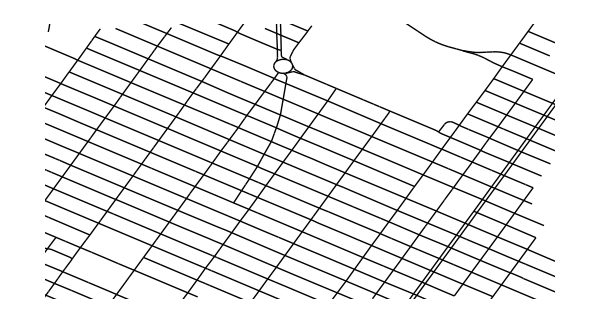

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
GeoGraphics[Values[Line[Values[openStreetMapRegion[["Nodes",#Nodes,"Position"]]]]&/@Select[openStreetMapRegion["Ways"],MatchQ[#[["Tags","highway"]],"residential"|"primary"|"secondary"|"tertiary"|"motorway"|"trunk"]&]]];

generateLines[openStreetMapData_]:=Values[Line[Values[openStreetMapData[["Nodes",#Nodes,"Position"]]]]&/@Select[openStreetMapData["Ways"],MatchQ[#[["Tags","highway"]],"residential"|"primary"|"secondary"|"tertiary"|"motorway"|"trunk"]&]]/.
GeoPosition[{a_,b_}]:>{b,a}

Graphics[generateLines[openStreetMapRegion]]
Graphics[generateLines[openStreetMapRegion]/. GeoPosition[{lat_,lon_}]:>{lon,lat},PlotRange->{{-73.994,-73.968},{40.756,40.770}},(*your region bounds*)ImageSize->600]


ImagePartition[Graphics[generateLines[openStreetMapRegion]/. GeoPosition[{lat_,lon_}]:>{lon,lat},PlotRange->{{-73.994,-73.968},{40.756,40.770}},(*your region bounds*)ImageSize->600]
, 75]
```

```mathematica
nodeIDs=way["Nodes"]
```

way[Nodes]

```mathematica
osmNewYork=ResourceFunction["OSMImport"][GeoBoundsRegion[{{40.755905,40.769988},{-73.994486,-73.968818}}]];
```

```mathematica
Select[osmNewYork["Ways"], MatchQ[#[["Tags","highway"]],"residential"|"primary"|"secondary"|"tertiary"|"motorway"|"trunk"]&]
osmNewYork["Ways"][[1]]["Nodes"]
```

{42424773,427850877,1695371007,427850880,42424774,427850882,427850883,427850885,427850886,1806430566,1806430425,1806430504,1806430410,11149329065,427850887}

```mathematica
osmNewYork["Nodes"][[1;;3]]
```

<|666→<|Position→GeoPosition[{40.7642,-73.9923}],Tags→<|alt_name→Clinton,ele→9,gnis:feature_id→2042281,name→Hell's Kitchen,name:azb→هلز کیچن,name:fa→هلز کیچن,name:ja→ヘルズ・キッチン,name:ko→헬스키친,name:ru→Хэллс-Китчен,name:sr→Хелс кичен,name:sr-Latn→Hels kičen,name:uk→Гелс-Кітчен,name:zh→地獄廚房,place→suburb|>|>,42421969→<|Position→GeoPosition[{40.7693,-73.9811}],Tags→<|direction→forward,highway→traffic_signals|>|>,42421972→<|Position→GeoPosition[{40.7698,-73.9822}],Tags→<|highway→traffic_signals,traffic_signals:direction→forward|>|>|>